```mathematica
(*Load the CSV file*)
data=Import[NotebookDirectory[]<>"data-fopt-fit.csv"];

(*Extract and clean column names from the first row*)
columnNames=StringTrim/@First[data];

(*Remove the header row to isolate the data*)
data=Rest[data];

(*Print column names to check*)
Print[columnNames];
```

{vw,alpha,betaH,Tn,f_p,Om_p,at,bt,rbt,s0t,omega_0t,K}

```mathematica
(*Assign each column to a separate variable using safe access to Position*)
vw=If[Length[Position[columnNames,"vw"]]>0,data[[All,Position[columnNames,"vw"][[1,1]]]],{}];
alpha=If[Length[Position[columnNames,"alpha"]]>0,data[[All,Position[columnNames,"alpha"][[1,1]]]],{}];
betaH=If[Length[Position[columnNames,"betaH"]]>0,data[[All,Position[columnNames,"betaH"][[1,1]]]],{}];
Tn=If[Length[Position[columnNames,"Tn"]]>0,data[[All,Position[columnNames,"Tn"][[1,1]]]],{}];
fp=If[Length[Position[columnNames,"f_p"]]>0,data[[All,Position[columnNames,"f_p"][[1,1]]]],{}];
Omp=If[Length[Position[columnNames,"Om_p"]]>0,data[[All,Position[columnNames,"Om_p"][[1,1]]]],{}];
at=If[Length[Position[columnNames,"at"]]>0,data[[All,Position[columnNames,"at"][[1,1]]]],{}];
bt=If[Length[Position[columnNames,"bt"]]>0,data[[All,Position[columnNames,"bt"][[1,1]]]],{}];
rbt=If[Length[Position[columnNames,"rbt"]]>0,data[[All,Position[columnNames,"rbt"][[1,1]]]],{}];
s0t=If[Length[Position[columnNames,"s0t"]]>0,data[[All,Position[columnNames,"s0t"][[1,1]]]],{}];
omega0t=If[Length[Position[columnNames,"omega_0t"]]>0,data[[All,Position[columnNames,"omega_0t"][[1,1]]]],{}];
K=If[Length[Position[columnNames,"K"]]>0,data[[All,Position[columnNames,"K"][[1,1]]]],{}];
```

```mathematica
(*Define the data points*)
dataVWAlphaFP=Transpose[{vw,alpha,fp}];
dataVWAlphaOmP=Transpose[{vw,alpha,Omp}];
dataVWAlphaAt=Transpose[{vw,alpha,at}];
dataVWAlphaBt=Transpose[{vw,alpha,bt}];
dataVWAlphaRbt=Transpose[{vw,alpha,rbt}];
dataVWAlphaS0t=Transpose[{vw,alpha,s0t}];
dataVWAlphaOmega0t=Transpose[{vw,alpha,omega0t}];
dataVWAlphaK=Transpose[{vw,alpha,K}];
```

```mathematica
(*Create interpolating functions*)
intFP=Interpolation[dataVWAlphaFP,InterpolationOrder->1];
intOmP=Interpolation[dataVWAlphaOmP,InterpolationOrder->1];
intAt=Interpolation[dataVWAlphaAt,InterpolationOrder->1];
intBt=Interpolation[dataVWAlphaBt,InterpolationOrder->1];
intRbt=Interpolation[dataVWAlphaRbt,InterpolationOrder->1];
intS0t=Interpolation[dataVWAlphaS0t,InterpolationOrder->1];
intOmega0t=Interpolation[dataVWAlphaOmega0t,InterpolationOrder->1];
intK=Interpolation[dataVWAlphaK,InterpolationOrder->1];
```

```mathematica
(*Evaluate at a point*)
vw0=0.5;
alpha0=0.5;
fp0=intFP[vw0,alpha0];
at0=intAt[vw0,alpha0];
bt0=intBt[vw0,alpha0];
rbt0=intRbt[vw0,alpha0];
s0t0=intS0t[vw0,alpha0];
Omegap0=intOmega0t[vw0,alpha0];
K0=intK[vw0,alpha0];

(*Degrees of freedom*)
gstarData=Import[NotebookDirectory[]<>"gstar.txt","Table"];
gHighTemp={{1.*10^14*gstarData[[1,1]],gstarData[[1,2]]}};
dataG1=Join[gHighTemp,gstarData];
TData=dataG1[[All,1]];
gstarData=dataG1[[All,2]];
gstarFun=Interpolation[Transpose[{TData,gstarData}]];

(*Frequency domain*)
fdomainDefault=10^Range[-24,24,48/999]//N;

(*Generating fit parameters from the interpolated function*)
fb0=rbt0*fp0;
(*This part can be modified based on different nucleation tamperatures and bubble nucleation rates.*)
betaHDefault=1;
betaHNew=10;
TnDefault=100;
TnNew=1000;

rstarDefault=(8 π)^(1/3)*vw0/betaHDefault;
rstarNew=(8 π)^(1/3)*vw0/betaHNew;
gstarDefault=gstarFun[TnDefault];
gstarNew=gstarFun[TnNew];

xDefault=rstarDefault/(K0^(1/2));
JDefault=rstarDefault*(1-1/(1+2*xDefault)^(1/2));
FgwDefault=3.57*10^-5*(100/gstarDefault)^(1/3);
xNew=rstarNew/(K0^(1/2));
JNew=rstarNew*(1-1/(1+2*xNew)^(1/2));
FgwNew=3.57*10^-5*(100/gstarNew)^(1/3);

f0Default=2.6*10^-6*(TnDefault/100)*(gstarDefault/100)^(1/6);
kR=fdomainDefault*(rstarDefault/f0Default);
```

```mathematica
(*GW spectrum-default*)
omegaFitDefault=Omegap0*(fdomainDefault/s0t0)^9*((2+rbt0^(-12+bt0))/((fdomainDefault/s0t0)^at0+(fdomainDefault/s0t0)^bt0+rbt0^(-12+bt0)*(fdomainDefault/s0t0)^12));//Quiet
```

```mathematica
f0New=2.6*10^-6*(TnNew/100)*(gstarNew/100)^(1/6);
fdomainNew=kR/(rstarNew/f0New);
omegaFitNew=(omegaFitDefault/(FgwDefault*JDefault))*(FgwNew*JNew);
```

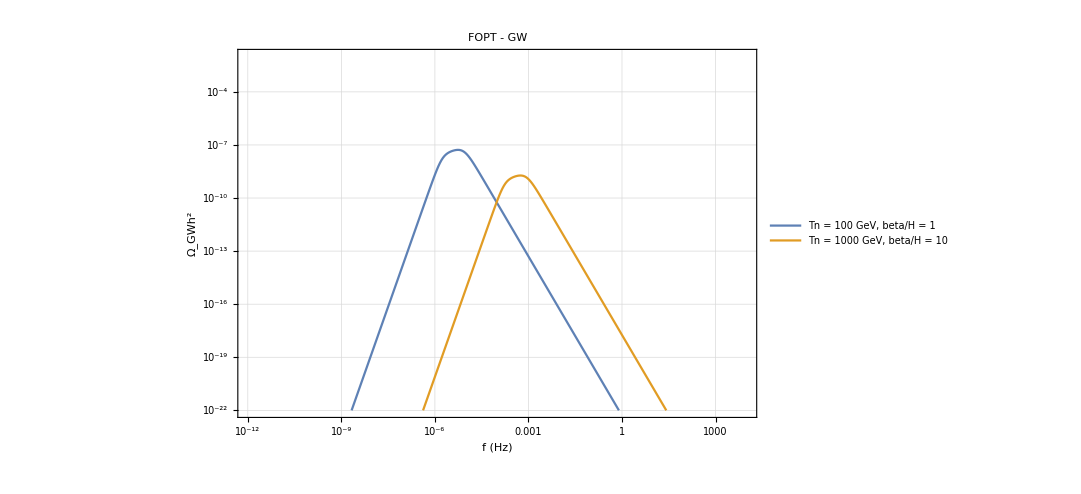

```mathematica
(*Plotting*)
ListLogLogPlot[{Transpose[{fdomainDefault,omegaFitDefault}],Transpose[{fdomainNew,omegaFitNew}]},PlotRange->{{1.*10^-12,1.*10^4},{1.*10^-22,1.*10^-2}},Frame->True,FrameLabel->{"f (Hz)","\!\(\*SubscriptBox[\(Ω\), \(GW\)]\)\!\(\*SuperscriptBox[\(h\), \(2\)]\)"},PlotLabel->"FOPT - GW",GridLines->Automatic,Joined->True,PlotLegends->{"Tn = 100 GeV, beta/H = 1","Tn = 1000 GeV, beta/H = 10"},FrameStyle->18,ImageSize->800]
```